## Preliminary

```mathematica
Solve[2^x==2121990148,x][[1,1,2,1,2]]//N
```

30.9828

```mathematica
10Log[.04]
```

-32.1888

```mathematica
508848.7162 -0.6643597983+(1.7716261288/2)-0.015944//FullForm
508848.7162 +1.1072663305-(1.7716261288/2)-0.015944-.0344//FullForm
```

```mathematica
508848.92170926614
```

508849.

```mathematica
508332.46-0.664+(1.7716/2)-.118//FullForm
```

```mathematica
508332.5638
```

```mathematica
5088
```

```mathematica
%-508849.019
```

-0.540197

713281.74

## Plotting

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True];
```

```mathematica
wm8Data=Import["/Volumes/ni_lab/wavemeterEightChannelLogs/wm8Data.csv","CSV"]
```

{{Timestamp,Channel 1 Frequency (GHz),Channel 1 Saturation,Channel 2 Frequency (GHz),Channel 2 Saturation,Channel 3 Frequency (GHz),Channel 3 Saturation,Channel 4 Frequency (GHz),Channel 4 Saturation,Channel 5 Frequency (GHz),Channel 5 Saturation,Channel 6 Frequency (GHz),Channel 6 Saturation,Channel 7 Frequency (GHz),Channel 7 Saturation,Channel 8 Frequency (GHz),Channel 8 Saturation},613684,{2021-11-01T13:55:32.854,374676.,-20.8821,0,-inf,508849.,-24.4856,0,-inf,0,-inf,0,-inf,295177.,-18.9379,713290.,-16.0571}}
 |  |  |  |

```mathematica
time=AbsoluteTime/@wm8Data[[2;;,1]]-AbsoluteTime[wm8Data[[2,1]]];
prepList[timeList0_,list0_,column0_]:=Module[{timeList=timeList0,list=list0,column=column0},
DeleteCases[Transpose@{timeList,list[[2;;,column]]},x_/;x[[2]]==0]
]
freqs=Table[prepList[time,wm8Data,i],{i,2,16,2}];
sats=Table[prepList[time,wm8Data,i],{i,3,17,2}];
```

```mathematica
Table[Mean[freqs[[i]]][[2]],{i,1,8}]//Quiet//FullForm
```

List[370159.,51086.4,508849.,328970.,Part[Mean[List[]],2],252860.,295178.,713316.]

```mathematica
ListPlot[freqs[[1]]]
```

$Aborted

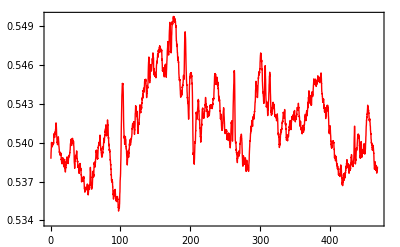

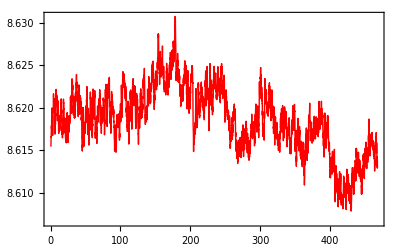

```mathematica
{timeData3,fData3}=Transpose[freqs[[3]]];
ListPlot[Transpose@{timeData3[[6;;-5]],MovingAverage[fData3-508848.47880273394,10]}]
{timeData8,fData8}=Transpose[freqs[[8]]];
ListPlot[Transpose@{timeData8[[6;;-5]],MovingAverage[fData8-713281.74,10]}]
```

```mathematica
{timeData3,fData3}=Transpose[freqs[[3]]];
```

```mathematica
wmError=fData3-508848.47880273394;
```

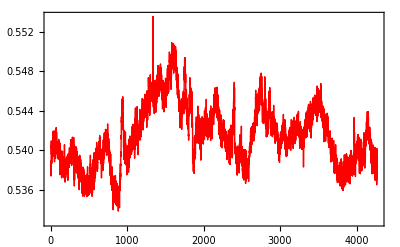

```mathematica
ListPlot[wmError]
```

```mathematica
meanShift[channel0_,α10_,α70_,α80_]:=Module[{channel=channel0,α1=α10,α7=α70,α8=α80},
α={α1,1,1,1,1,1,α7,α8};
{timeData,fData}=Transpose[freqs[[channel]]];
{Transpose@{timeData,fData-α[[channel]](Mean[freqs[[channel]]][[2]])/(Mean[freqs[[3]]][[2]])(wmError)-Mean[fData-α[[channel]](Mean[freqs[[channel]]][[2]])/(Mean[freqs[[3]]][[2]])(wmError)]},Total[(fData-α[[channel]](Mean[freqs[[channel]]][[2]])/(Mean[freqs[[3]]][[2]])(wmError)-Mean[fData-α[[channel]](Mean[freqs[[channel]]][[2]])/(Mean[freqs[[3]]][[2]])(wmError)])^2]}]
{ListPlot[Table[meanShift[i,1,.8,.5][[1]],{i,{8}}],ImageSize->1000,AspectRatio->1/3,PlotRange->All],Table[meanShift[i,1,1,1][[2]],{i,{1,3,7,8}}]}
```

Thread::tdlen: Objects of unequal length in {713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,«18»,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,«384376»}+{«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in «1» cannot be combined.

Transpose::nmtx: The first two levels of {{1932.03,1932.13,1932.24,1932.35,1932.5,1932.57,1932.67,1932.87,1933.,1933.11,1933.26,1938.37,1938.54,1938.58,1938.68,1938.91,1939.01,«18»,1941.18,1941.21,1941.31,1941.42,1941.57,1941.64,1941.75,1941.94,1941.97,1942.07,1942.18,1942.32,1942.4,1942.51,1942.69,«384376»},«1»} cannot be transposed.

Thread::tdlen: Objects of unequal length in {713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,«18»,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,713292.,«384376»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted[]

$Aborted

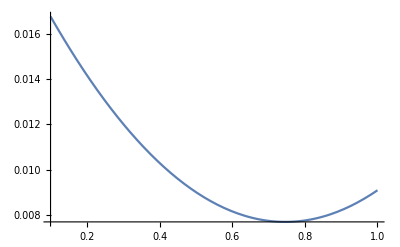

```mathematica
Plot[meanShift[1,α1,1,1][[2]],{α1,0.1,1}]
```